```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-up-xi1-pi-noD-L.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgf=Interpolation[Flatten[Hdgu,1]];
Herf=Interpolation[Flatten[Heru,1]];
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-dleta-pi-xi1-L.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;

dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;


dHerf=Interpolation[Flatten[dHeru,1]];


dEerf=Interpolation[Flatten[dEeru,1]];

Dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-D-xi1-pi-L.wdx"];

DHeru=Query[1,2]@Dgpdu;
DHdau=Query[1,3]@Dgpdu;

DEeru=Query[2,2]@Dgpdu;
DEdau=Query[2,3]@Dgpdu;

DHerf=Interpolation[Flatten[DHeru,1]];
dDgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-dleta-D-pi-xi1-L.wdx"];

dDHeru=Query[1,2]@dDgpdu;


dDEeru=Query[2,2]@dDgpdu;


dDHerf=Interpolation[Flatten[dDHeru,1]];
```

```mathematica
(*先把上面的结果组合起来*)
```

```mathematica
Hdgall[x_,t_]:=Hdgf[x,t];
Herall[x_,t_]:=Herf[x,t]+dHerf[x,t]+DHerf[x,t]+dDHerf[x,t];
```

```mathematica
(*u quark*)
```

```mathematica
(*Λ k+,只需要乘上系数，u=sbar=pi+的结果*)
Coep1=(-I)*(Dc+3Fc)^2/(12*(0.093)^2*2*(2Pi)^4);
(*k+的u贡献，分段但就是总的*)
lHdg[x_,t_]=Coep1*Hdgall[x,t];
lHer[x_,t_]=Coep1*Herall[x,t];
lEdg[x_,t_]=Coep1*Edgall[x,t];
lEer[x_,t_]=Coep1*Eerall[x,t];
(*k0没有u夸克*)
(*图的u夸克总结果，就是对粒子求和*)
Hdgzall[x_,t_]=lHdg[x,-t];
Herallwhole[x_,t_]=lHer[x,-t];
Edgzall[x_,t_]=lEdg[x,-t];
Eerallwhole[x_,t_]=lEer[x,-t];
```

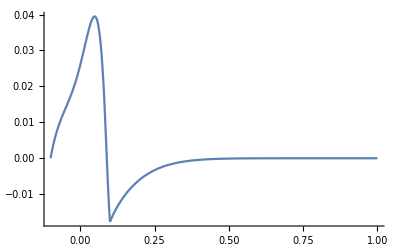

```mathematica
Show[Plot[Hdgzall[x,1],{x,0.1,1},PlotRange->All],Plot[Herallwhole[x,1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
Herallwhole[0.05,1]
```

0.0394296+0. ⅈ

```mathematica
(*s quark*)
```

```mathematica
(*k+,sbar=u*)
lHdgs[x_,t_]=-lHdg[-x,t];
lHers[x_,t_]=-lHer[-x,t];
lEdgs[x_,t_]=-lEdg[-x,t];
lEers[x_,t_]=-lEer[-x,t];
(*图的总结果，就是对粒子求和*)
Hdgfalls[x_,t_]=lHdgs[x,-t];
Herallwholes[x_,t_]=lHers[x,-t];
Edgfalls[x_,t_]=lEdgs[x,-t];
Eerallwholes[x_,t_]=lEers[x,-t];
```

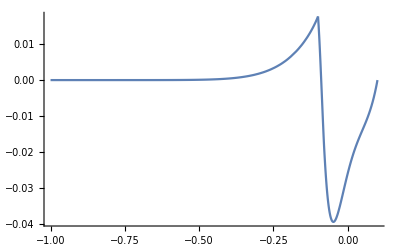

```mathematica
Show[Plot[Hdgfalls[x,1],{x,-1,-0.1},PlotRange->All],Plot[Herallwholes[x,1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
pathu=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"u-diagram-d-L.wdx"}];
paths=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"s-diagram-d-L.wdx"}];
outu=<|"H"-><|"DGz"->Hdgzall[x,t],"ER"->Herallwhole[x,t],"DGf"->0|>|>;
outs=<|"H"-><|"DGz"->0,"ER"->Herallwholes[x,t],"DGf"->Hdgfalls[x,t]|>|>;
Export[pathu,outu]
Export[paths,outs]
```

G:\calc-online\gpd\drawpic\baryon\gpd\result\u-diagram-d-L.wdx

G:\calc-online\gpd\drawpic\baryon\gpd\result\s-diagram-d-L.wdx